Rice, chapter 5: Diffusion Theory

Kolmogorov forward: equilibrium distribution

```mathematica
ClearAll[M,V,psi,wbar,p,Ne,u1,u2]
```

```mathematica
M[p_]:=(p(1-p)/(2wbar[p]))*(D[wbar[p],p])-u1*p+u2(1-p);
```

```mathematica
V[p_]:=p*(1-p)/(2*Ne);
```

```mathematica
forward=D[V[p]*psi[p],p]==2*M[p]*psi[p];
```

```mathematica
sol=DSolve[forward,psi[p],p]//FullSimplify
```

{{psi[p]→(1-p)^(-1+4 Ne u1) p^(-1+4 Ne u2) C[1] wbar[p]^(2 Ne)}}

mutation and drift:

```mathematica
ψ[c_,wbar_,Ne_,p_,u1_,u2_]:=c*(wbar^(2Ne))*((1-p)^((4Ne*u1)-1))*(p^((4Ne*u2)-1))
```

```mathematica
ψ[1,1,Ne,p,u,u]
```

(1-p)^(-1+4 Ne u) p^(-1+4 Ne u)

```mathematica
Manipulate[Plot[ψ[1,1,Ne,p,u,u],{p,0,1}], {Ne,0,100}, {u,0,0.3}]
```

```mathematica
ψmd[p_,θ_]:=(p(1-p))^(θ-1)
```

```mathematica
θ[Ne_,u_]:= 4*Ne*u
```

```mathematica
Manipulate[Plot[ψmd[p,θ],{p,0,1}], {θ,0,10}]
```

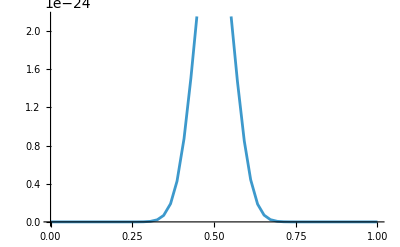

```mathematica
Plot[f[p]=(p-p^2)^(40-1),{p,0,1}]
```

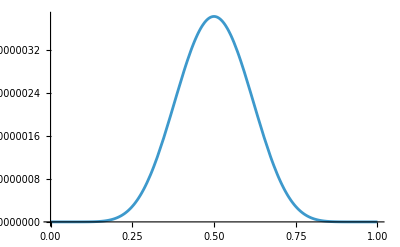

```mathematica
Plot[f[p]=(p-p^2)^(10-1),{p,0,1}]
```

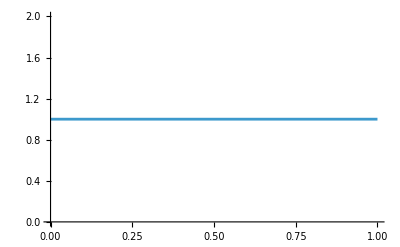

```mathematica
Plot[f[p]=(p-p^2)^(1-1),{p,0,1}]
```

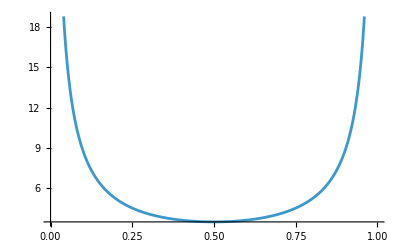

```mathematica
Plot[f[p]=(p-p^2)^(0.1-1),{p,0,1}]
```

selection and drift:

```mathematica
wbar[p_,w11_,w12_,w22_]:= (p^2)w11 + 2p(1-p)w12 + ((1-p)^2)w22
```

-heterozygote advantage (balancing selection)

```mathematica
Simplify[wbar[p,1,1+s,1]]
```

1+2 p s-2 p^2 s

```mathematica
wbar1[p_,s_]:= E^(2s*p(1-p))
```

```mathematica
ψ[c,wbar1[p,s],Ne,p,u1,u2]
```

c (ⅇ^(2 (1-p) p s))^(2 Ne) (1-p)^(-1+4 Ne u1) p^(-1+4 Ne u2)

```mathematica
ψ[1,wbar1[p,s],Ne,p,0,0]
```

((ⅇ^(2 (1-p) p s))^(2 Ne))/((1-p) p)

```mathematica
Manipulate[Plot[ψ[1,wbar1[p,s],Ne,p,0,0],{p,0,1}], {Ne,0,10}, {s,0,1}]
```

```mathematica
ψsd[p_,Nes_]:=E^(4Nes*p(1-p))/(p(1-p))
```

```mathematica
Manipulate[Plot[ψsd[p,Nes],{p,0,1}], {Nes,0,10}]
```

```mathematica
Plot[ψsd[p,40],{p,0,1},PlotRange->All]
```

-Graphics-

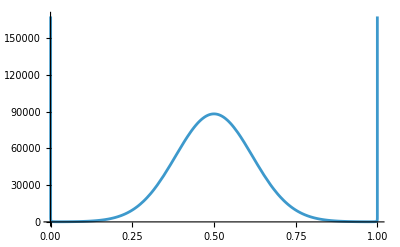

```mathematica
Plot[ψsd[p,10],{p,0,1}]
```

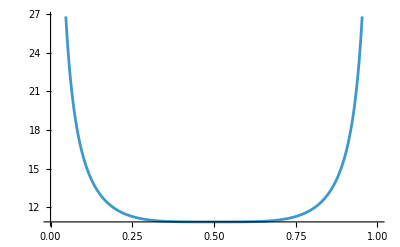

```mathematica
Plot[ψsd[p,1],{p,0,1}]
```

- heterozygote intermediate (directional selection)

```mathematica
Simplify[wbar[p,1+2s,1+s,1]]
```

1+2 p s

```mathematica
wbar2[p_,s_]:= E^(2s*p)
```

```mathematica
ψ[c,wbar2[p,s],Ne,p,u1,u2]
```

c (ⅇ^(2 p s))^(2 Ne) (1-p)^(-1+4 Ne u1) p^(-1+4 Ne u2)

```mathematica
ψ[1,wbar2[p,s],Ne,p,0,0]
```

((ⅇ^(2 p s))^(2 Ne))/((1-p) p)

```mathematica
Manipulate[Plot[ψ[1,wbar2[p,s],Ne,p,0,0],{p,0,1}], {Ne,0,10},{s,0,1}]
```

```mathematica
ψds[p_,Nes_]:=E^(4Nes*p)/(p(1-p))
```

```mathematica
Manipulate[Plot[ψds[p,Nes],{p,0,1}], {Nes,0,10}]
```

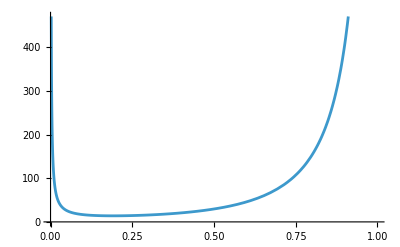

```mathematica
Plot[ψds[p,1],{p,0,1}]
```

```mathematica
Plot[ψds[p,10],{p,0,1}]
```

-Graphics-

```mathematica
Plot[ψds[p,40],{p,0,1}]
```

-Graphics-

mutation, selection, and drift:

```mathematica
phat[u_,s_]:=Sqrt[u/s]
```

```mathematica
Simplify[wbar[p,1-s,1,1]]
```

1-p^2 s

```mathematica
wbar3[p_,s_]:= E^(-s*p^2)
```

```mathematica
ψ[c,wbar3[p,s],Ne,p,u1,u2]
```

c (ⅇ^(-p^2 s))^(2 Ne) (1-p)^(-1+4 Ne u1) p^(-1+4 Ne u2)

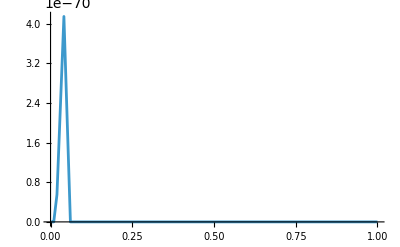

```mathematica
Plot[ψ[1,wbar3[p,0.01],1000000,p,10^(-5),10^(-5)],{p,0,1},PlotRange->All]
```

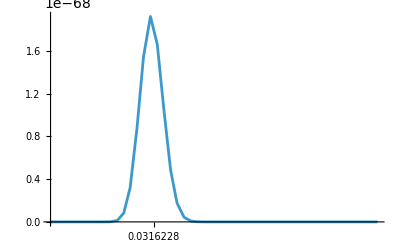

```mathematica
Plot[ψ[1,wbar3[p,0.01],1000000,p,10^(-5),10^(-5)],{p,0,0.1},Ticks->{{phat[10^(-5),0.01]},Automatic},PlotRange->All]
```

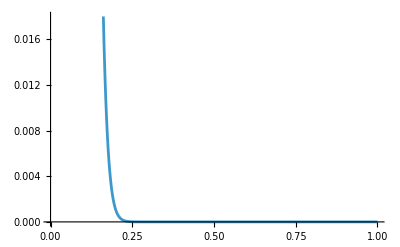

```mathematica
Plot[ψ[1,wbar3[p,0.01],10000,p,10^(-5),10^(-5)],{p,0,1}]
```

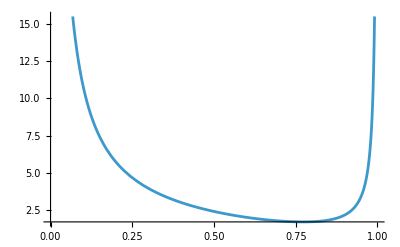

```mathematica
Plot[ψ[1,wbar3[p,0.01],100,p,10^(-5),10^(-5)],{p,0,1}]
```

migration between populations:
- migration maintaining variation (neutral allele)

```mathematica
ClearAll[M,V,psi,wbar,p,Ne,u1,u2,m]
```

```mathematica
ψ[c_,wbar_,Ne_,p_,u1_,u2_,m_,p1_]:=c*(wbar^(2Ne))*((1-p)^((4Ne*(u1+m-m*p1))-1))*(p^((4Ne*(u2+m*p1))-1))
```

```mathematica
ψ[c,wbar,Ne,p,u1,u2,m,p1]
```

c (1-p)^(-1+4 Ne (m-m p1+u1)) p^(-1+4 Ne (m p1+u2)) wbar^(2 Ne)

```mathematica
ψ[1,1,Ne,p,u1,u2,m,0.5]
```

(1-p)^(-1+4 Ne (0.5 m+u1)) p^(-1+4 Ne (0.5 m+u2))

```mathematica
ψ[1,1,Ne,p,0,0,m,0.5]
```

(1-p)^(-1+2. m Ne) p^(-1+2. m Ne)

```mathematica
ψm[p_,Nem_]:=(p(1-p))^((2Nem)-1)
```

```mathematica
Manipulate[Plot[ψm[p,Nem],{p,0,1}], {Nem,0,5}]
```

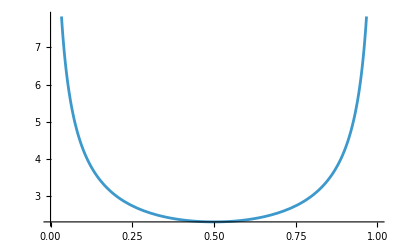

```mathematica
Plot[ψm[p,0.2],{p,0,1}]
```

```mathematica
Plot[ψm[p,0.5],{p,0,1}]
```

-Graphics-

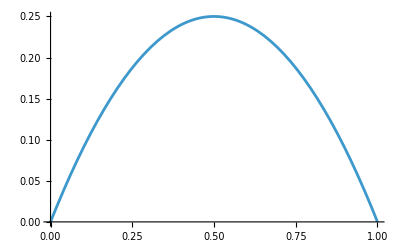

```mathematica
Plot[ψm[p,1],{p,0,1}]
```

```mathematica
Plot[ψm[p,5],{p,0,1}]
```

-Graphics-

-migration opposing selection

```mathematica
ψ[1,wbar2[p,s],Ne,p,0,0,m,0]
```

((ⅇ^(2 p s))^(2 Ne) (1-p)^(-1+4 m Ne))/p

```mathematica
Manipulate[Plot[ψ[1,wbar2[p,s],Ne,p,0,0,m,0],{p,0,1}], {s,0,0.5}, {Ne,0,40}, {m,0,0.5}]
```

```mathematica
ψmos[p_,Nes_,Nem_]:=(E^((4Nes*p )+(4Nem*Log[1-p]))/(p(1-p)))
```

```mathematica
Manipulate[Plot[ψmos[p,Nes,Nem],{p,0,1}], {Nes,4,20}, {Nem,2,10}]
```

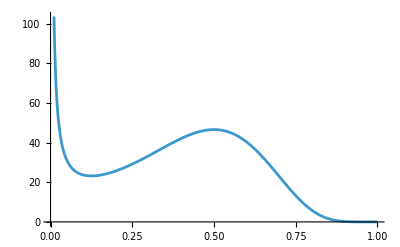

```mathematica
Plot[ψmos[p,4,2],{p,0,1}]
```

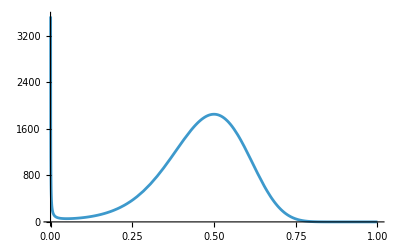

```mathematica
Plot[ψmos[p,10,5],{p,0,1}]
```

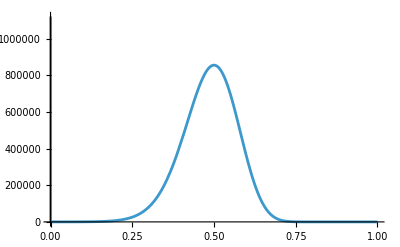

```mathematica
Plot[ψmos[p,20,10],{p,0,1}]
```

Kolmogorov backward : equilibrium distribution

```mathematica
wbar[p_,w11_,w12_,w22_]:= (p^2)w11 + 2p(1-p)w12 + ((1-p)^2)w22
```

```mathematica
backward=D[F[p0],p0]==-(2*M[p0]/V[p0])*F[p0];
```

```mathematica
sol=DSolve[backward,F[p0],p0]//FullSimplify
```

{{F[p0]→ⅇ^(-(2 M[K[1]])/V[K[1]]K[1]1p0) C[1]}}

-probability of fixation: not completely recessive

```mathematica
u[p0_]:= (Integrate[E^(-Integrate[2M/V[p0],p0]),{p0,0,p0}])/(Integrate[E^(-Integrate[2M/V[p0],p0]),{p0,0,1}])
```

```mathematica
w=ReplaceAll[Collect[wbar[p,1+s,1+h*s,1],p],p^2->0]//Simplify
```

1+2 h p s

```mathematica
dw=D[w,p]
```

2 h s

```mathematica
Clear[M]
```

```mathematica
M[p_,w_,dw_,u1_,u2_]:=(p*(1-p)/(2*w))*dw-u1*p+u2*(1-p);
```

```mathematica
V[p_]:=p*(1-p)/(2*Ne);
```

```mathematica
M[p,w,dw,0,0]
```

(h (1-p) p s)/(1+2 h p s)

```mathematica
m1=ReplaceAll[M[p,w,dw,0,0],2h*s*p->0]
```

h (1-p) p s

```mathematica
Integrate[2*m1/V[p],p]
```

4 h Ne p s

```mathematica
Integrate[E^(-4 h*Ne*p0*s),{p0,0,p0}]
```

-(-1+ⅇ^(-4 h Ne p0 s))/(4 h Ne s)

```mathematica
u[p0_]:= (Integrate[E^(-4 h*Ne*p*s),{p,0,p0}])/(Integrate[E^(-4 h*Ne*p*s),{p,0,1}])
```

```mathematica
u[p0]
```

(-1+ⅇ^(-4 h Ne p0 s))/(-1+ⅇ^(-4 h Ne s))

```mathematica
Limit[u[p0],s->0]
```

p0

```mathematica
u[1/(2*N)]
```

(-1+ⅇ^(-(2 h Ne s)/N))/(-1+ⅇ^(-4 h Ne s))

```mathematica
Evaluate[u[1/(2 Ne)]/. {h->1,s->x}]
```

(-1+ⅇ^(-2 x))/(-1+ⅇ^(-4 Ne x))

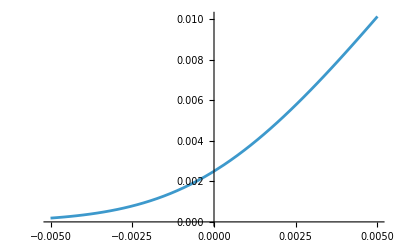

```mathematica
Plot[Evaluate[u[1/(2 Ne)]/. {h->1,s->x,Ne->200}],{x,-0.005,0.005}]
```

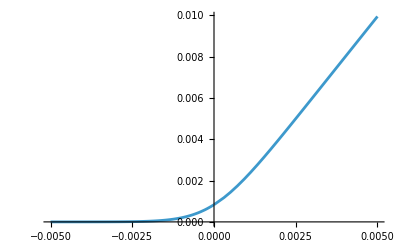

```mathematica
Plot[Evaluate[u[1/(2 Ne)]/. {h->1,s->x,Ne->600}],{x,-0.005,0.005}]
```

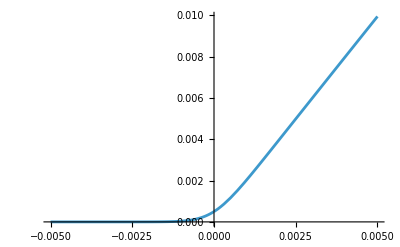

```mathematica
Plot[Evaluate[u[1/(2 Ne)]/. {h->1,s->x,Ne->1000}],{x,-0.005,0.005}]
```

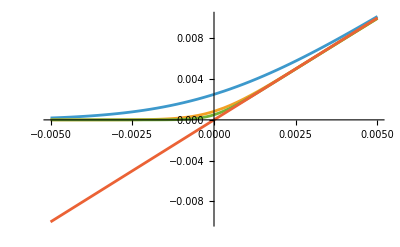

```mathematica
Plot[{Evaluate[u[1/(2 Ne)]/. {h->1,s->x,Ne->200}],Evaluate[u[1/(2 Ne)]/. {h->1,s->x,Ne->600}],Evaluate[u[1/(2 Ne)]/. {h->1,s->x,Ne->1000}],y=2x},{x,-0.005,0.005}]
```

-completely recessive

```mathematica
w2=wbar[p,1+s,1,1]//Simplify
```

1+p^2 s

```mathematica
dw2=D[w2,p]
```

2 p s

```mathematica
M[p,w2,dw2,0,0]
```

((1-p) p^2 s)/(1+p^2 s)

```mathematica
m=ReplaceAll[M[p,w2,dw2,0,0],1+s*(p^2)->1]
```

(1-p) p^2 s

```mathematica
Integrate[2*m/V[p],p]
```

2 Ne p^2 s

```mathematica
u[p0_]:= (Integrate[E^(-2Ne*(p^2)*s).08,{p,0,p0}])/(Integrate[E^(-2Ne*(p^2)*s),{p,0,1}])
```

```mathematica
u[1/(2*N)]
```

(.08 Erf[(√Ne √s)/(√2 N)])/Erf[√2 √Ne √s]

```mathematica
git["cap5"]
```

Sincronizado com o GitHub!

<|ExitCode→0,StandardOutput→branch 'main' set up to track 'origin/main'.
,StandardError→To https://github.com/aliceab14/projetos-mathematica.git
   7128d45..076ff9f  HEAD -> main
|>